# Practica 2: Sistema de ecuaciones con matrices

## 2.1 Resolución de sistemas de ecuaciones de 2x2

Resuelva analiticamente y graficamente los siguientes sistemas de ecuaciones con dos incognitas

				a.   x-y=1	b.      x-y=2	   c.   x-y=1
				     x+y=3	     2x-2y=4	         x-y=3

### Inciso a

```mathematica
Solve[{x-y==1,x+y==3},{x,y}]
```

{{x→2,y→1}}

```mathematica
Reduce[{x-y==1,x+y==3},{x,y}]
```

x==2&&y==1

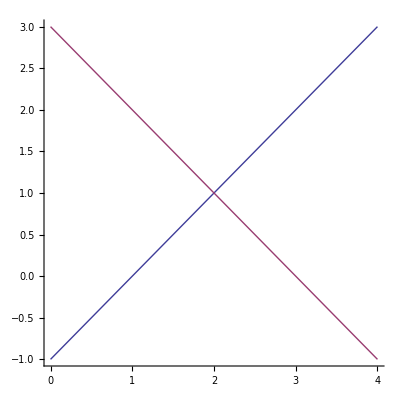

```mathematica
ContourPlot[{x-y==1,x+y==3},{x,0,4},{y,-1,3},Axes->True,Frame->False]
```

### Inciso b

```mathematica
Solve[{x-y==2,2x-2y==4},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→2+y}}

```mathematica
Reduce[{x-y==2,2x-2y==4},{x,y}]
```

y==-2+x

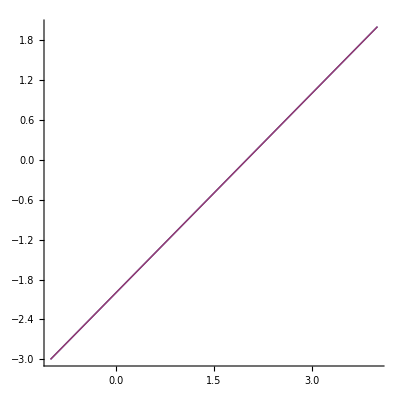

```mathematica
ContourPlot[{x-y==2,2x-2y==4},{x,-1,4},{y,-3,2},Axes->True,Frame->False]
```

### Inciso c

```mathematica
Solve[{x-y==1,x-y==3},{x,y}]
```

{}

```mathematica
Reduce[{x-y==1,x-y==3},{x,y}]
```

False

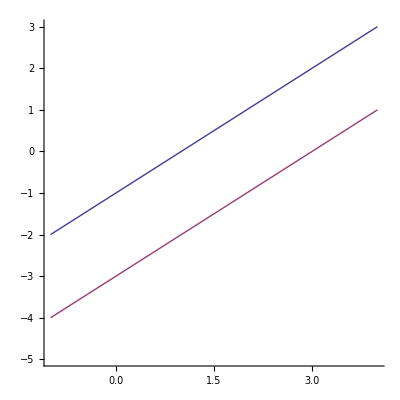

```mathematica
ContourPlot[{x-y==1,x-y==3},{x,-1,4},{y,-5,3},Axes->True,Frame->False]
```

## 2.2 Resolución de sistemas de ecuaciones de 3x3

Considere los siguientes sistema de ecuaciones

	               	   a.   3x+4y+z =1			b.   3x-2y-z =-2
			        2x+3y     =0			       x-y+3z=5
		                   4x+3y-z  =-2			      -x+y+z=-1

Lo resolveremos de TRES formas distintas, con Solve, LinearSolve y RowReduce.

### Inciso a

```mathematica
Solve[{3x+4y+z==1,2x+3y==0,4x+3y-z==-2},{x,y,z}]
```

{{x→-3/7,y→2/7,z→8/7}}

```mathematica
A=({{3, 4, 1}, {2, 3, 0}, {4, 3, -1}});    B=({{1}, {0}, {-2}});
```

```mathematica
LinearSolve[A,B]  // MatrixForm
```

(-3/7
2/7
8/7)

```mathematica
f=({{3, 4, 1, 1}, {2, 3, 0, 0}, {4, 3, -1, -2}});
```

```mathematica
RowReduce[f]  // MatrixForm
```

(1 | 0 | 0 | -3/7
0 | 1 | 0 | 2/7
0 | 0 | 1 | 8/7)

```mathematica
Clear[A,B,f]
```

### Inciso b

```mathematica
Solve[{3x-2y-z==-2,x-y+3z==5,-x+y+z==-1},{x,y,z}]
```

{{x→-5,y→-7,z→1}}

```mathematica
A=({{3, -2, -1}, {1, -1, 3}, {-1, 1, 1}});    B=({{-2}, {5}, {-1}});
```

```mathematica
LinearSolve[A,B]  // MatrixForm
```

(-5
-7
1)

```mathematica
f=({{3, -2, -1, -2}, {1, -1, 3, 5}, {-1, 1, 1, -1}});
```

```mathematica
RowReduce[f] // MatrixForm
```

(1 | 0 | 0 | -5
0 | 1 | 0 | -7
0 | 0 | 1 | 1)

```mathematica
Clear[A,B,f]
```

## Ejemplos de sistemas de ecuaciones de 3x3

Considere los siguientes sistema de ecuaciones

	               	   a.   x+2y      =-3			b.   x+3y-z =4
			        2x+3y-2z=-10			    -2x+y+3z=9
		                   -x+6z      =9			     4x+2y+z=11

Resuelvalo de TRES formas distintas.

### Inciso a

```mathematica
Solve[{x+2y==-3,2x+3y-2z==-10,-x+6z==9},{x,y,z}]
```

{{x→-15,y→6,z→-1}}

```mathematica
A=({{1, 2, 0}, {2, 3, -2}, {-1, 0, 6}});    B=({{-3}, {-10}, {9}});
```

```mathematica
LinearSolve[A,B]  // MatrixForm
```

(-15
6
-1)

```mathematica
f=({{1, 2, 0, -3}, {2, 3, -2, -10}, {-1, 0, 6, 9}});
```

```mathematica
RowReduce[f]  // MatrixForm
```

(1 | 0 | 0 | -15
0 | 1 | 0 | 6
0 | 0 | 1 | -1)

```mathematica
Clear[A,B,f]
```

### Inciso b

```mathematica
Solve[{x+3y-z==4,-2x+y+3z==9,4x+2y+z==11},{x,y,z}]
```

{{x→1,y→2,z→3}}

```mathematica
A=({{1, 3, -1}, {-2, 1, 3}, {4, 2, 1}});    b=({{4}, {9}, {11}});
```

```mathematica
LinearSolve[A,b]  // MatrixForm
```

(1
2
3)

```mathematica
B=({{1, 3, -1, 4}, {-2, 1, 3, 9}, {4, 2, 1, 11}});
```

```mathematica
RowReduce[B]  // MatrixForm
```

(1 | 0 | 0 | 1
0 | 1 | 0 | 2
0 | 0 | 1 | 3)

```mathematica
p1=Plot3D[x+3y-4,{x,0,4},{y,0,4},AxesLabel->{x,y,z},Boxed->False]
```

-Graphics3D-

```mathematica
p2=Plot3D[3+(2/3)x-(1/3)y,{x,0,4},{y,0,4},AxesLabel->{x,y,z},Boxed->False]
```

-Graphics3D-

```mathematica
p3=Plot3D[11-4x-2y,{x,0,4},{y,0,4},AxesLabel->{x,y,z},Boxed->False]
```

-Graphics3D-

```mathematica
Show[{p1,p2,p3},ViewPoint->{2.037, -2.381, 1.279}]
```

-Graphics3D-

```mathematica
Clear[A,B,p1,p2,p3]
```

## 2.3 Resolución de sistemas de ecuaciones de nxn y nxm

Considere los siguientes sistemas de ecuaciones

		a.  2x+y-3z=-3		b.    x+2y-z=2 		c.   x+3y+5z+10w=0  
		    3x+y-5z=5		    2x+5y-3z=1 	    -x       -2z  -4w=0
	   	   -2x+y+5z=-35	      x+4y-3z=3		    2x+4y+8z+16w=0
	   	   							y+ z+ 2w=0 

Una forma de resolverlo es usar Solve y Reduce

### Inciso a

```mathematica
Solve[{2x+y-3z==-3,3x+y-5z==5,-2x+y+5z==-35},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→8+2 z,y→-19-z}}

```mathematica
Reduce[{2x+y-3z==-3,3x+y-5z==5,-2x+y+5z==-35},{x,y,z}]
```

y==-15-x/2&&z==-4+x/2

### Inciso b

```mathematica
Solve[{x+2y-z==2,2x+5y-3z==1,x+4y-3z==3},{x,y,z}]
```

{}

```mathematica
Reduce[{x+2y-z==2,2x+5y-3z==1,x+4y-3z==3},{x,y,z}]
```

False

### Inciso c

```mathematica
Solve[{x+3y+5z+10w==0,-x-2z-4w==0,2x+4y+8z+16w==0,y+z+2w==0},{x,y,z,w}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→-4 w-2 z,y→-2 w-z}}

```mathematica
Reduce[{x+3y+5z+10w==0,-x-2z-4w==0,2x+4y+8z+16w==0,y+z+2w==0},{x,y,z,w}]
```

y==x/2&&w==-x/4-z/2

## Ejemplos de sistemas de ecuaciones de nxm

Considere los siguientes sistemas de ecuaciones

		a.  x-3y+z-t=-2		b.    x+y=3 		c.   x+2y-z=2  
		   -x+3y+2z=-2		    2x+ay=0 		    2x+3y+5z=5
	   							     -x-3y+8z=-1 

Una forma de resolverlo es usar Solve y Reduce

### Inciso a

```mathematica
Solve[{x-3y+z-t==-2,-x+3y+2z==-2},{x,y,z,t}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→-2/3+(2 t)/3+3 y,z→-4/3+t/3}}

```mathematica
Reduce[{x-3y+z-t==-2,-x+3y+2z==-2},{x,y,z,t}]
```

z==-1+x/2-(3 y)/2&&t==1+(3 x)/2-(9 y)/2

### Inciso b

```mathematica
Reduce[{x+y==3,2x+a y==0},{x,y},Backsubstitution->True]
```

-2+a≠0&&x==(3 a)/(-2+a)&&y==-6/(-2+a)

```mathematica
Solve[{x+y==3,2x+a y==0},{x,y}]
```

{{x→(3 a)/(-2+a),y→-6/(-2+a)}}

### Inciso c

```mathematica
Reduce[{x+2y-z==2,2x+3y+5z==5,-x-3y+8z==-1},{x,y,z}]
```

y==15/13-(7 x)/13&&z==4/13-x/13

```mathematica
Solve[{x+2y-z==2,2x+3y+5z==5,-x-3y+8z==-1},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→4-13 z,y→-1+7 z}}

```mathematica
A=({{1, 2, -1}, {2, 3, 5}, {-1, -3, 8}});    b=({{2}, {5}, {-1}});
```

```mathematica
LinearSolve[A,b] (*Mathematica le da un valor arbitrario a z, en este ejemplo z=0*)  // MatrixForm
```

(4
-1
0)

```mathematica
Clear[A,b]
```

```mathematica
A=({{1, 2, -1, 2}, {2, 3, 5, 5}, {-1, -3, 8, -1}});
```

```mathematica
RowReduce[A]  // MatrixForm
```

(1 | 0 | 13 | 4
0 | 1 | -7 | -1
0 | 0 | 0 | 0)

```mathematica
Clear[A]
```